# Simple Task 5

Brian Carlson 2-12-14

## Problem 1.

```mathematica
addDigits[start_,stop_]:=Module[{lst={},i},(*First, we declare the local variables to be used, *)
For[i=start,i≤ stop, (*We set the range for the loop, *)
AppendTo[lst,{i,Total[IntegerDigits[i]]}]; (*Here, we take the sum of the digits for each value of i and add them to our list, lst, to be returned*)
i++
]; (*Use a semicolon to suppress "null" output from the "For" loop.*)
Return[lst]
]
```

```mathematica
addDigits[187,203]
```

{{187,16},{188,17},{189,18},{190,10},{191,11},{192,12},{193,13},{194,14},{195,15},{196,16},{197,17},{198,18},{199,19},{200,2},{201,3},{202,4},{203,5}}

## Problem 2.

```mathematica
plotPoints[points_]:=
ListPlot[{points,points,Cases[points,{a_,4}|{a_,7}]},(*We separate the points, {x,y}, for which y is equal to 4 or 7*)
Joined->{True,False,False},
(*We set the styles for each list of points*)
PlotStyle->{Green,Directive[PointSize[Medium],Red],Directive[PointSize[Large],Yellow]},PlotLegends->SwatchLegend[{Green,Red,Yellow},{"Line","Y-values not equal to 0 or 7","Y-values equal to 0 or 7"},LegendMarkers->Graphics[{EdgeForm[Black],Rectangle[]}],LegendLabel->"Legend",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5]]
```

```mathematica
ST5lst={{0,5},{1,6},{2,5},{3,4},{4,3},{5,4},{6,5},{7,4},{8,3},{9,4},{10,5},{11,6},{12,7},{13,6},{14,7},{15,6},{16,5},{17,4},{18,5},{19,4},{20,5}};
```

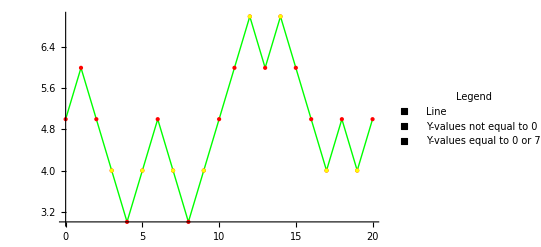

```mathematica
plotPoints[ST5lst]
```